# Gamma matrices, Schwinger-Dyson equations, and the SYK model

Abdel Elabd, June 2023
Following:
- https://www.youtube.com/watch?v=sU-_3BTftrY
- https://arxiv.org/abs/1711.08482
- https://arxiv.org/abs/1806.06840

## 1. Define fermions

The starting point is that bosons commute and fermions anticommute (the latter having something to do with the Dirac equation, but we won’t get into that). We state here without proof that, to define our fermions, the simply must satisfy the Clifford algebra:
(1)         

Define          
 (2)         {c_i,c_j^†}==δ_ij

The algebra in (2) is equivalent to the algebra in (1), and also defines the canonical anticommutation relations for fermionic modes. So we interpret  as fermionic modes of a field.

We will work backwards, first defining the  operators that satisfy the algebra in (2); from those we can extract the  operators that satisfy (1), i.e. our fermions.

### a. Define fermionic modes

```mathematica
SeedRandom[0];
ℕ=24;
Nc = ℕ/2;
cr = {{0, 1}, {0, 0}}; 
an ={{0, 0}, {1, 0}};
id = IdentityMatrix[2];
id2 = {{-1, 0}, {0, 1}};
c[n_] := SparseArray[KroneckerProduct @@ (Table[id, {n-1}]~Join~{cr}~Join~Table[id2,{Nc-n}])]
cd[n_] := SparseArray[KroneckerProduct @@ (Table[id, {n-1}]~Join~{an}~Join~Table[id2,{Nc-n}])]
```

Check that these fermionic modes indeed satisfy the algebra in (2):

```mathematica
c[1].c[1]+c[1].c[1] //MatrixForm;
c[1].c[2]+c[2].c[1] //MatrixForm;
cd[1].cd[1]+cd[1].cd[1] //MatrixForm;
cd[1].cd[2]+cd[2].cd[1] //MatrixForm;
c[1].cd[1]+cd[1].c[1]//MatrixForm;
c[1].cd[2]+cd[2].c[1]//MatrixForm;
```

#### Notes from meeting:

,   . That is what’s happening above, reproduce analytically. If the different 2x2 blocks commuted, you would only need parentheses/2, but since they anticommute you need to multiply them by , which (in 2D) is like the identity matrix but with the first element flipped in sign, hence the anticommutation.  
Note: ,

### b. Define fermions

Now we can find . Since each one is expensive to compute and will be called upon many times, it’s more efficient to precompute a look-up table for the first K states of both  and .

```mathematica
Do[ψ[n]=1/(√2)(c[n]+cd[n]), {n,Nc}]//Timing
Do[ψ[Nc+n]=1/(√2)(-I c[n]+I cd[n]), {n, Nc}]//Timing
```

{2.85938,Null}

{4.79688,Null}

Don’t read too closely into the specific locations of the precomputed values. Analytically, there’s no relation - this is just a simple and efficient way to allocate the precomputed values of  to a lookup-table.

## 2. Defining the Hamiltonian

An SYK model with q-order coupling has couplings between groups of q fermions at a time. It’s Hamiltonian is given by:
(4)

Here, we are interested in the regular SYK model (as opposed to the Brownian SYK model), so the coupling constants  are time-independent, and normally/Gaussian distributed with mean 0 and variance  (see 2nd or 3rd reference for why this specific variance).

 gives the overall strength of the coupling, or “sets the energy scale of the system”.

#### Notes from meeting:

Question: Greater  means greater variance in the coupling constants. Does greater variance in the coupling constants mean a greater average separation between energy eigenvalues? And does that mean a greater “spread” i.e. a larger uncertainty i.e.  a higher-entropy system?

Answer from Gustavo:  What’s important to look for is whether the temperature () is greater than or less than . Therefore, an important magnitude to study is . 

Moreover: Although the couplings are random,  itself is not necessarily a random matrix. All we’re saying is that, if the system exhibits chaotic behavior, it’s late-time statistics (i.e. the statistics of the eigenvalues and eigenvalue-spacing of ) should follow those of a random matrix.

### a. Hamiltonian with q=2

For q=2, the Hamiltonian is given by:
(5)   

We want a coupling coefficient for each pairwise connection between the existing fermions, i.e. N^2 = NxN coefficients.

```mathematica
q2=2;
𝔍2 = 1;
js2 = RandomVariate[NormalDistribution[0,√(𝔍2^2 ((q2-1)!)/ℕ^(q2-1))],{ℕ, ℕ}, WorkingPrecision -> 100];
```

Moreover, we can precompute the inner-product of every pair of fermions.

```mathematica
Do[ψ2[i1,i2]=ψ[i1].ψ[i2], {i1, ℕ}, {i2,i1+1,ℕ}]//Timing
```

{0.265625,Null}

And then it’s pretty straightforward to compute the Hamiltonian.

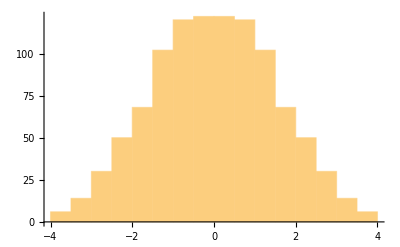

```mathematica
H2= I Sum[js2[[i1, i2]] ψ2[i1,i2], {i1, ℕ}, {i2, i1+1, ℕ}]//Normal;
iv2 = H2//N//Eigenvalues//Sort;
Histogram[iv2]
```

### b. Hamiltonian with q=4

(6)

Generate coupling constants

```mathematica
q4=4;
𝔍4= 4;
js4 = RandomVariate[NormalDistribution[0,√(𝔍4^2 ((q4-1)!)/ℕ^(q4-1))],{ℕ, ℕ, ℕ, ℕ}, WorkingPrecision -> 100];
```

Precompute inner products.

```mathematica
Do[ψ4[i1,i2,i3,i4] = ψ2[i1,i2].ψ2[i3,i4], {i1, ℕ}, {i2, i1+1, ℕ}, {i3, i2+1, ℕ}, {i4, i3+1, ℕ}]//Timing
```

{2.21875,Null}

Compute Hamiltonian

```mathematica
H4 = I^(q4/2) Sum[js4[[i1,i2,i3,i4]] ψ4[i1, i2, i3, i4], {i1, ℕ}, {i2, i1+1, ℕ}, {i3, i2+1, ℕ}, {i4, i3+1, ℕ}]//Timing
```

{33.2656,SparseArray[<2301952>, {4096, 4096}]}

```mathematica
iv4 = H4//N//Eigenvalues//Sort;
iv4//Histogram
```

Histogram::ldata: Eigenvalues[-0.0970091 ψ2[1.,2.].ψ2[3.,4.]+«15»+«10616»] is not a valid dataset or list of datasets.

Looks like it’s approaching a semicircle distribution, but in the video he says it’s not for some reason.

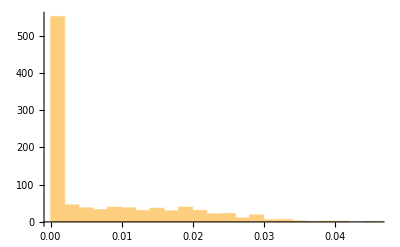

```mathematica
div4 = Differences[iv4];
div4//Histogram
```

Time-allowing: try out N=24, q=6.

## 4. 2-point functions

With an explicit analytical Hamiltonian in hand, there’s nothing we can’t do. 

For example, we can compute the correlator between fermions  and , separated by a time .
(7)   , where  if   and  if .

```mathematica
β=1;
H = H4//N;
𝔍 = 𝔍4;
q = q4;
Clear[Gn];
Gn[a_,b_,τ_,β_,λ_] := Gn[a,b,τ,β,λ] = Block[{},
If[τ>0,
Eτ = MatrixExp[-τ H λ];
Eβτ = MatrixExp[(-β+τ)H λ];
Tr[Eβτ.ψ[a].Eτ.ψ[b]]/Tr[Eβτ.Eτ],
Eτ = MatrixExp[+τ H λ];
Eβτ = MatrixExp[(-β-τ)H λ];
-Tr[Eβτ.ψ[b].Eτ.ψ[a]]/Tr[Eβτ.Eτ],
]
]
```

### a. Exact self-correlator in time

Not sure exactly why (obviously it has something to do with being spin-1/2), but the 2-point function of a fermion w.r.t. itself is antiperiodic. So that will serve here as a good check:

```mathematica
Dynamic[tt]
tbGweak = Table[{tt,Gn[1,1,tt,1,1]}, {tt,-1/2,1/2,1/10}]//Re;
```

The following is why I hate Mathematica syntax

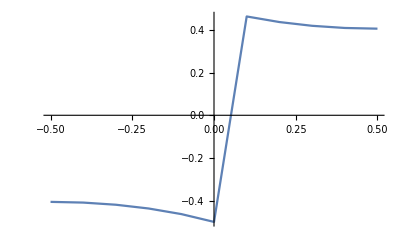

```mathematica
lp = {tbGweak}//ListPlot[#, Joined->True]&
```

### b. Schwinger-Dyson equations: approximate self-correlator in time, in the large-N limit

For the time self-correlator computed in section 4.a, the relevant Schwinger-Dyson equations are:
(8)    
(9)    
These basically define the behavior in the  limit. 


We’re going to numerically approximate the solution to this system of equations, through iteration:
First plug in the zero-th order approximation, , into . This returns . Next, plug in  into  to get the first-order approximation of . Plug this first-order  into  to get first-order  and first-order , which in turn gives us the second-order approximation of , and so on and so forth until the series converges. The series is guaranteed to converge for small-enough J. 

Note: Just because the series doesn’t numerically converge doesn’t mean it’s not solvable. Apparently there are a bunch of tricks you can apply to achieve convergence in different regimes, but he doesn’t go into detail. 

Below, we define  and  explicitly, and  and  as Fourier transforms.

```mathematica
β=1;
Λ = 10;
slω =ω -> (2π)/β(n+1/2);
sln = n -> (ω β)/(2π)-1/2;
Clear[G, Σ, Gτ]; 
Σ[0,n_]=0;
G[i_, nn_] := -1/(I ω + Σ[i, nn]) /.slω /.n ->nn;
Gτ[i_,τ_?NumericQ] := Gτ[i,τ]=1/2 Sign[τ]+1/β Sum[Exp[-I ω τ/.slω] (G[i,n]-G[0,n])//N, {n, -Λ,Λ}]
Σ[i_,nn_] := Σ[i,nn] = NIntegrate[𝔍^2 Gτ[i-1,τ]^(q-1) Exp[I ω τ  /.slω] /.n->nn, {τ, -β/2, β/2}]
```

We can plot, say, the first 10 iterations to (inductively) confirm that it does converge.

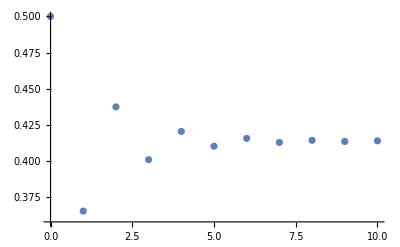

```mathematica
Table[{n, Gτ[n,1/4]}, {n,0,10}]//Re//ListPlot
```

Let’s compare this to what we got in section 4.a:

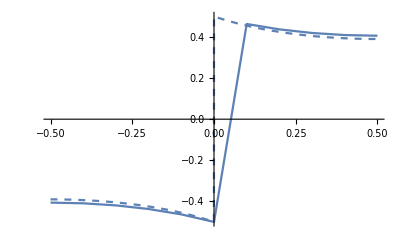

```mathematica
Show[Plot[Gτ[11,t]//Re, {t,-β/2,β/2}, PlotStyle->Dashed],lp]
```

Dashed line is approximate  solution, solid line is the exact  solution.

Suggested exercises: Get them to match (i.e. find the value of N, and the order of iteration, at which the approximate and exact solutions are indistinguishable. Moreover, see how this varies with q). Play with parameters (e.g. stronger or weaker overall coupling J, i.e. energy level). I’m most interested in messing with q.